Testing Spatial Audio on a Single Plane - 2D

## Determining Delay with Dist. to Ears

Graphical Visualization

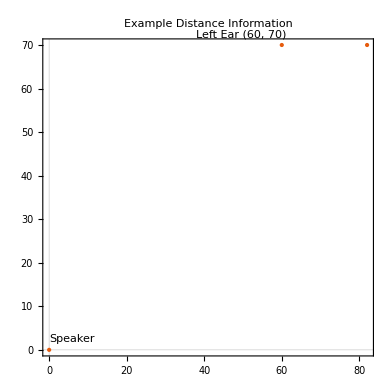

```mathematica
ListPlot[{
Labeled[{0,0},"Speaker"],
Labeled[{60,70}, "Left Ear (60, 70)"],
Labeled[{82,70}, "Right Ear (62, 70)"]
},
PlotTheme->"Scientific",
(*PlotRange->{{0,100},{0,100}},*)
PlotStyle->PointSize[Large],
ScalingFunctions->{Identity,Identity}, 
AspectRatio->1,
PlotRangePadding->10,
PlotLabel->"Example Distance Information"]
```

Assigning Attributes

```mathematica
distanceLeftEar = Quantity[√(60.^2+70.^2),"centimeters"]
distanceRightEar = Quantity[√(62.^2+70.^2), "centimeters"]
(*Angle Between Speaker and X-axis when connected as Right Triangle with Ear*)
thetaLeftEar =Quantity[ArcTan[70./60.] ,"radians"]
thetaRightEar =Quantity[ArcTan[70./62.], "radians"]
```

92.1954 cm

93.5094 cm

0.86217 rad

0.84593 rad

Speed of Sound

```mathematica
speedOfSound =StandardAtmosphereData[Quantity[0, "feet"],"SoundSpeed"]
```

340.29 m/s

Determining Delays

```mathematica
delayLeftEar=distanceLeftEar/speedOfSound
delayRightEar = distanceRightEar / speedOfSound
```

0.00270932 s

0.00274793 s

## Working with Audio Functions to Channel Delay

```mathematica
sampleAudio=Import["/Users/shubhamkumar/Downloads/prenks/Serene Queen - LDR.mp3"]
```

```mathematica
(*Doesn't Work, Stereo not split into Mono for each Channel*)
AudioChannelSeparate[sampleAudio]
```

{,}

Visualizing Audio and Trimming For Faster Processing

-Graphics-

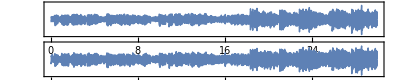

2

```mathematica
sampleAudioTrimmed = AudioTrim[sampleAudio, {10,40}]
Spectrogram[sampleAudioTrimmed]
AudioPlot[sampleAudioTrimmed]
AudioChannels[sampleAudioTrimmed]
```

Panning Test

```mathematica
leftAudio = AudioPan[sampleAudioTrimmed,-1.]
rightAudio = AudioPan[sampleAudioTrimmed, 1.]
```

```mathematica
AudioChannelCombine[{leftAudio, rightAudio}]
```

Delaying Audio For Each Channel

```mathematica
delayedLeftAudio = AudioDelay[leftAudio,delayLeftEar]
delayedRightAudio= AudioDelay[rightAudio,delayRightEar]
(*Making Sure Delay Worked*)
Duration@{delayedLeftAudio, delayedRightAudio, leftAudio, rightAudio}
```

{30.0027 s,30.0027 s,30. s,30. s}

```mathematica
spatial2dAudioTrimmed = AudioChannelCombine[{delayedRightAudio, delayedLeftAudio}]
```

Checking Differences

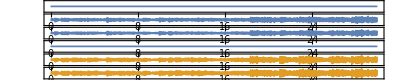

{4,2}

```mathematica
AudioPlot@{spatial2dAudioTrimmed, sampleAudioTrimmed}
AudioChannels@{spatial2dAudioTrimmed, sampleAudioTrimmed}
```

## Functional Implementation

Combining Processes from Previous Sections + Adding in Audio Amplification

```mathematica
Plot2dAudio[speakerPoint_, leftEar_, rightEar_]:=
Module[{speakerPointLoc=speakerPoint, leftEarPointLoc=leftEar, rightEarPointLoc=rightEar},
(*Bruh why do arrays start at 1*)
(*Print[speakerPointLoc[[0]]];*)
ListPlot[{
Labeled[{speakerPointLoc[[1]], speakerPointLoc[[2]]},"Speaker"],
Labeled[{leftEarPointLoc[[1]], leftEarPointLoc[[2]]}, "Left Ear"],
Labeled[{rightEarPointLoc[[1]], rightEarPointLoc[[2]]}, "Right Ear"]
},
PlotTheme->"Scientific",
(*PlotRange->{{0,100},{0,100}},*)
PlotStyle->PointSize[Large],
ScalingFunctions->{Identity,Identity}, 
AspectRatio->1,
PlotRangePadding->10,
PlotLabel->"Distance Information"]
]
```

```mathematica
Point2dAudio[file_, speakerPoint_, leftEar_, rightEar_, amplificationProportion_]:=
Module[{fileLoc=file, speakerPointLoc=speakerPoint, leftEarPointLoc=leftEar, rightEarPointLoc=rightEar, k=amplificationProportion},
(*Trimming Raw Audio & Separating Audio for each Channel*)
rawAudioData = Import[fileLoc];
trimmedRawAudioData = AudioNormalize[AudioTrim[rawAudioData,{0, 30}]];
leftAudioData = AudioPan[trimmedRawAudioData,-1.];
rightAudioData = AudioPan[trimmedRawAudioData, 1.];

(*Calculating Delays*)
leftEarDistanceFromSpeaker = Quantity[√((leftEarPointLoc[[1]]-speakerPointLoc[[1]])^2.+(leftEarPointLoc[[2]]-speakerPointLoc[[2]])^2.), "centimeters"];
rightEarDistanceFromSpeaker = Quantity[√((rightEarPointLoc[[1]]-speakerPointLoc[[1]])^2.+(rightEarPointLoc[[2]]-speakerPointLoc[[2]])^2.), "centimeters"];
speedOfSound = StandardAtmosphereData[Quantity[0, "feet"],"SoundSpeed"];
leftEarAudioDelay = leftEarDistanceFromSpeaker/speedOfSound;
rightEarAudioDelay = rightEarDistanceFromSpeaker/speedOfSound;

(*Debug*)
Print["Left Ear Audio Distance:"]; Print[leftEarDistanceFromSpeaker];
Print["Right Ear Audio Distance:"]; Print[rightEarDistanceFromSpeaker];
Print["Left Ear Audio Delay:"]; Print[leftEarAudioDelay];
Print["Right Ear Audio Delay:"]; Print[rightEarAudioDelay];

(*Audio Delaying & Attenuation*)
leftEarAudioDelayedData = AudioAmplify[AudioDelay[leftAudioData, leftEarAudioDelay], QuantityMagnitude[k/leftEarDistanceFromSpeaker]];
rightEarAudioDelayedData = AudioAmplify[AudioDelay[rightAudioData, rightEarAudioDelay], QuantityMagnitude[k/rightEarDistanceFromSpeaker]];


(*Mixing to Generate Final Sound*)
AudioNormalize[AudioChannelCombine[{leftEarAudioDelayedData, rightEarAudioDelayedData}]]
]
```

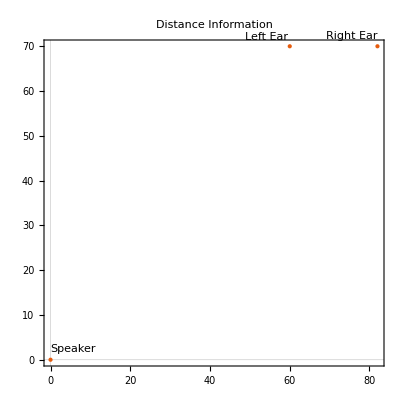

```mathematica
Plot2dAudio[{0,0},{60,70},{82,70}]
```

Function Unit Tests

```mathematica
delayTest = Point2dAudio["/Users/shubhamkumar/Downloads/prenks/Thunder - LDR.mp3",{0,0},{60,70},{82,70}, 90]
```

Left Ear Audio Distance:

92.1954 cm

Right Ear Audio Distance:

107.815 cm

Left Ear Audio Delay:

0.00270932 s

Right Ear Audio Delay:

0.00316832 s

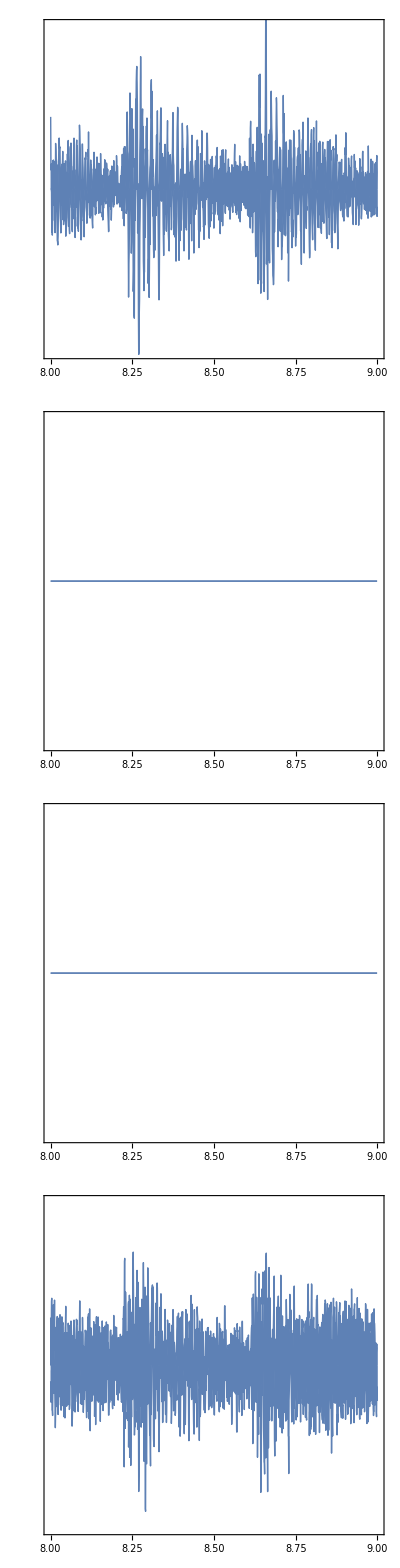

-Graphics-

4

```mathematica
AudioPlot[delayTest, PlotRange->{{8,9},{-0.8, 0.8}}]
Spectrogram[delayTest]
AudioChannels[delayTest]
```

```mathematica
delayTestLoudness =AudioLoudness[delayTest]
```

TimeSeries[…]

Comparing With Raw Audio - Can’t Quite Tell a Difference but the Audio Plot Shows that there is.

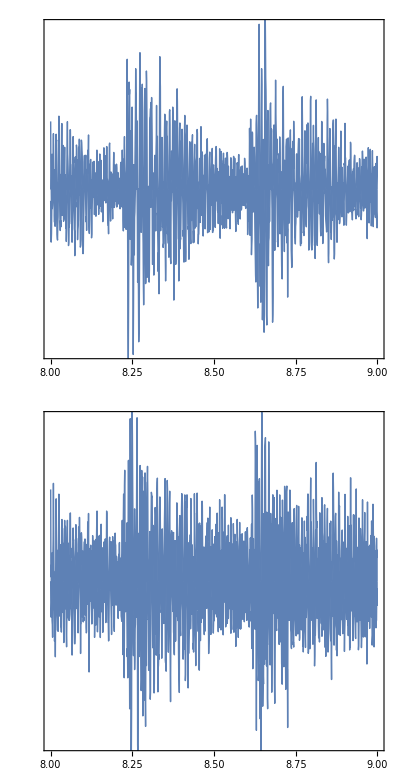

```mathematica
rawAudioComparison=AudioNormalize[AudioTrim[Import["/Users/shubhamkumar/Downloads/prenks/Thunder - LDR.mp3"],{0,30}]]
AudioPlot[rawAudioComparison, PlotRange-> {{8,9},{-0.8, 0.8}}]
```

```mathematica
rawAudioLoudness =AudioLoudness[rawAudioComparison]
```

TimeSeries[…]

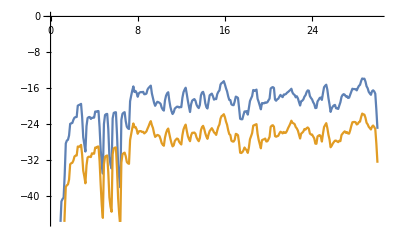

```mathematica
ListLinePlot@{rawAudioLoudness, delayTestLoudness}
```

## GUI Implementation